## Section | Transcendental Functions

The zeroth-order Bessel function J_0(z) can be expressed as an infinite sum (its Maclaurin series),

J_0(x)==∑_(k=0)^∞ 1/(k!)^2(-x^2/4)^k

### Zeros of J_0(z)

Plot J_0(x) over -15≤x≤15. What is the symmetry of this function? What is the approximate spacing of the roots of J_0(x)? [2 Marks]

Plot J_0(x) over -15≤x≤15.

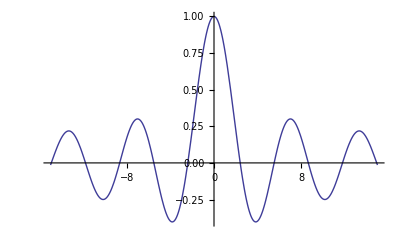

```mathematica
Plot[Subscript[J, 0](x),{x,-15,15}]
```

J_0(x) is even. The separation of the zeros is slightly larger than 3, approximately π.

Verify that the sum gives J_0(x)

Verify that the sum gives J_0(x):

```mathematica
Subscript[J, 0](x)==∑_(k=0)^∞ ((-x^2/4)^k)/(k!)^2
```

True

Use these observations with FindRoot to find accurate numerical values of the first 50 positive roots of J_0(x). Compare your values to the built-in function BesselJZero. [2 Marks]

Use FindRoot with initial guess spaced by π to obtain accurate numerical values of the first 50 positive roots of J_0(x):

```mathematica
𝒿=x/.FindRoot[Subscript[J, 0](x),{x,π Range[50]},WorkingPrecision->20]
```

{2.4048255576957727686,5.5200781102863106486,8.653727912911012217,11.791534439014281614,14.930917708487785948,18.071063967910922543,21.211636629879258959,24.352471530749302737,27.493479132040254796,30.634606468431975118,33.775820213573568684,36.91709835366404398,40.058425764628239295,43.199791713176730358,46.341188371661814019,49.482609897397817174,52.624051841114996029,55.765510755019979312,58.906983926080942133,62.048469190227169883,65.189964800206860441,68.331469329856798271,71.472981603593732825,74.614500643701837884,77.756025630388055038,80.897555871137627864,84.039090776938190158,87.180629843641153651,90.322172637210480056,93.463718781944774171,96.605267950996268778,99.74681985868059647,102.8883742541947946,106.02993091645161551,109.17148964980538355,112.31305028049490963,115.45461265366693963,118.59617663087253172,121.73774208795096297,124.87930891323294605,128.02087700600832408,131.16244627521391461,134.3040166383054661,137.44558802028427779,140.58716035285429655,143.72873357368973253,146.87030762579664959,150.01188245695475749,153.15345801922789249,156.29503426853352382}

Compare these values to the built-in function BesselJZero (note that you can use Range):

```mathematica
N[BesselJZero[0,Range[50]],20]
```

{2.4048255576957727686,5.5200781102863106496,8.653727912911012217,11.791534439014281614,14.930917708487785948,18.071063967910922543,21.211636629879258959,24.352471530749302737,27.493479132040254796,30.634606468431975118,33.775820213573568684,36.91709835366404398,40.058425764628239295,43.199791713176730358,46.341188371661814019,49.482609897397817174,52.624051841114996029,55.765510755019979312,58.906983926080942133,62.048469190227169883,65.189964800206860441,68.331469329856798271,71.472981603593732825,74.614500643701837884,77.756025630388055038,80.897555871137627864,84.039090776938190158,87.180629843641153651,90.322172637210480056,93.463718781944774171,96.605267950996268778,99.74681985868059647,102.8883742541947946,106.02993091645161551,109.17148964980538355,112.31305028049490963,115.45461265366693963,118.59617663087253172,121.73774208795096297,124.87930891323294605,128.02087700600832408,131.16244627521391461,134.3040166383054661,137.44558802028427779,140.58716035285429655,143.72873357368973253,146.87030762579664959,150.01188245695475749,153.15345801922789249,156.29503426853352382}

The agreement is excellent:

```mathematica
Abs[%-𝒿]
```

{0.,1.×10^-18,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
Union[Chop[%]]
```

{0}

### Product over roots of J_0(z)

J_0(x) can also be written as an infinite product (the Weierstrass–Hadamard factorization) over all the roots of J_0(x),

J_0(x)==∏_(k=1)^∞ (1-x^2/(0k)^2)

where 0k is the k^th positive zero of J_0(x).

Use Manipulate and Plot to compare J_0(x) to the finite product ∏_(k=1)^m (1-x^2/(0k)^2) for m=1,2,5,20,100. Hint: using pre-computed values of the roots will speed things up. [3 Marks]

Compute and save the first 100 roots:

```mathematica
𝒿=N[BesselJZero[0,Range[100]],20]
```

{2.4048255576957727686,5.5200781102863106496,8.653727912911012217,11.791534439014281614,14.930917708487785948,18.071063967910922543,21.211636629879258959,24.352471530749302737,27.493479132040254796,30.634606468431975118,33.775820213573568684,36.91709835366404398,40.058425764628239295,43.199791713176730358,46.341188371661814019,49.482609897397817174,52.624051841114996029,55.765510755019979312,58.906983926080942133,62.048469190227169883,65.189964800206860441,68.331469329856798271,71.472981603593732825,74.614500643701837884,77.756025630388055038,80.897555871137627864,84.039090776938190158,87.180629843641153651,90.322172637210480056,93.463718781944774171,96.605267950996268778,99.74681985868059647,102.8883742541947946,106.02993091645161551,109.17148964980538355,112.31305028049490963,115.45461265366693963,118.59617663087253172,121.73774208795096297,124.87930891323294605,128.02087700600832408,131.16244627521391461,134.3040166383054661,137.44558802028427779,140.58716035285429655,143.72873357368973253,146.87030762579664959,150.01188245695475749,153.15345801922789249,156.29503426853352382,159.43661116426314632,162.57818866894667752,165.71976674795502087,168.86134536923582569,172.00292450307820022,175.14450412190274307,178.28608420007377068,181.42766471373105079,184.56924564063871814,187.71082696004935978,190.85240865258152232,193.99399070010911979,197.13557308566141474,200.27715579333241178,203.41873880819864617,206.56032211624447366,209.7019057042940752,212.84348955994948275,215.98507367153401316,219.12665802804056747,222.26824261908431434,225.4098274348593299,228.5514124660988133,231.69299770403853878,234.83458314038324102,237.97616876727566286,241.11775457726802251,244.25934056329568256,247.40092671865282485,250.54251303696995547,253.684099512193081,256.82568613856441302,259.96727291060447157,263.10885982309547069,266.25044687106588012,269.39203404977606714,272.53362135470493145,275.67520878153745385,278.81679632615308658,281.95838398461491985,285.09997175315956454,288.24155962818769644,291.38314760625521224,294.52473568406495146,297.66632385845894252,300.80791212641113477,303.94950048502058111,307.09108893150503911,310.23267746319496095,313.37426607752784472}

The finite products are just polynomials:

```mathematica
∏_(k=1)^3 (1-x^2/𝒿_⟦k⟧^2)
```

(1-0.1729150690306449269 x^2) (1-0.03281780678206777423 x^2) (1-0.01335345132427233578 x^2)

Use Manipulate and Plot to compare J_0(x) to the finite product ∏_(k=1)^m (1-x^2/(0k)^2) for m=1,2,5,20,100, controlling the PlotRange and using Evaluate to speed up the plotting;

```mathematica
Manipulate[Plot[Evaluate[{Subscript[J, 0](x),∏_(k=1)^m (1-x^2/𝒿_⟦k⟧^2)}],{x,-15,15},PlotRange->1.1,AxesLabel->{x,Subscript[J, 0](x)}],{m,{1,2,5,20,100}},SaveDefinitions->True]
```

Expanding the sum and the product up to O(x^3),

J_0(x)==1-x^2/4+⋯==1-x^2∑_(k=1)^∞ 1/(0k)^2+⋯

which leads to

∑_(k=1)^∞ 1/(0k)^2==1/4

So, even though the 0k are the roots of a transcendental equation and cannot be written down in closed-form, this sum over the roots is simple and can be computed from the Maclaurin series expansion of J_0(x).

Check how well this sum is satisfied using the first 100 roots.

Use Total to compute the sum and compare to the exact result:

```mathematica
Abs[Total[1/𝒿^2]-1/4]
```

0.0010106758944169176

Alternatively, compute the sum directly:

```mathematica
4∑_(k=1)^100 1/(0k)^2//N
```

0.995957

Aside: taking the log of a product yields a sum. The logarithmic derivative of J_0(x) is

∂_x log(J_0(x))==(∂_z J_0(x))/(J_0(x))==2x∑_(k=1)^∞ 1/(x^2-(0k)^2)≡-2∑_(n=1)^∞ x^(2n-1)Z(2n)

where Z(n) is a sum over the roots.

Z(n)==∑_(k=1)^∞ 1/(0k)^n

*** There is also a section on the log-derivative in the Sums-Products Chapter ***

Compute the Maclaurin series of the logarithmic derivative of J_0(x):

```mathematica
-1/2 D[log(Subscript[J, 0](x)), x]+O[x]^10
```

x/4+x^3/32+x^5/192+(11 x^7)/12288+(19 x^9)/122880+O(x^10)

Check the value of Z(4)==1/32, computed using the first 100 roots:

```mathematica
Abs[N[∑_(k=1)^100 1/(0k)^4-1/32]]
```

3.39628×10^-9

### Example: Roots of the Airy function

The Airy function Ai(z) can be written as an infinite product over its roots,

Ai(z)==Ai(0)ⅇ^(z 0/0)∏_(n=1)^∞ (1-z/a_n)ⅇ^(z/a_n)

where a_n is the n^th zero of Ai(z). The logarithmic derivative of Ai(z) reads

(Ai'(z))/(Ai(z))==0/0-∑_(k=1)^∞ z^k Z(k+1)

where

Z(k)==∑_(n=1)^∞ 1/a_n^k

Plot z over -15≤z≤5. What do you observe about the location and spacing of the roots of z? [2 Marks]

Plot z over -15≤z≤5:

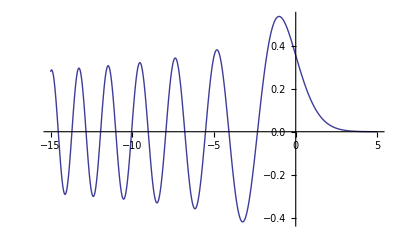

```mathematica
Plot[z,{z,-15,5}]
```

All the roots are negative and are getting closer together as z→-∞.

The zeros of the z are built-in as AiryAiZero. Use N to compute numerical values of the first 1000 roots. [1 Mark]

Compute numerical values of the first 1000 roots of z:

```mathematica
zeros=Table[AiryAiZero[n]//N,{n,1000}]
```

{-2.33811,-4.08795,-5.52056,-6.78671,-7.94413,-9.02265,-10.0402,-11.0085,-11.936,-12.8288,-13.6915,-14.5278,-15.3408,-16.1327,-16.9056,-17.6613,-18.4011,-19.1264,-19.8381,-20.5373,-21.2248,-21.9014,-22.5676,-23.2242,-23.8716,-24.5103,-25.1408,-25.7635,-26.3788,-26.987,-27.5884,-28.1833,-28.772,-29.3548,-29.9318,-30.5033,-31.0695,-31.6306,-32.1867,-32.7381,-33.2849,-33.8272,-34.3652,-34.8991,-35.4289,-35.9547,-36.4767,-36.9951,-37.5098,-38.021,-38.5288,-39.0333,-39.5345,-40.0326,-40.5276,-41.0196,-41.5087,-41.9948,-42.4782,-42.9589,-43.4369,-43.9123,-44.3851,-44.8554,-45.3233,-45.7887,-46.2518,-46.7126,-47.1711,-47.6274,-48.0816,-48.5336,-48.9835,-49.4314,-49.8772,-50.321,-50.7629,-51.2029,-51.641,-52.0773,-52.5117,-52.9443,-53.3752,-53.8044,-54.2318,-54.6576,-55.0817,-55.5042,-55.9251,-56.3444,-56.7621,-57.1784,-57.5931,-58.0063,-58.4181,-58.8284,-59.2373,-59.6447,-60.0508,-60.4556,-60.8589,-61.261,-61.6617,-62.0611,-62.4593,-62.8562,-63.2518,-63.6462,-64.0394,-64.4314,-64.8221,-65.2118,-65.6002,-65.9875,-66.3737,-66.7588,-67.1427,-67.5256,-67.9073,-68.288,-68.6677,-69.0463,-69.4238,-69.8004,-70.1759,-70.5504,-70.9239,-71.2965,-71.6681,-72.0387,-72.4084,-72.7771,-73.1449,-73.5117,-73.8777,-74.2428,-74.6069,-74.9702,-75.3326,-75.6941,-76.0548,-76.4146,-76.7735,-77.1317,-77.489,-77.8454,-78.2011,-78.556,-78.91,-79.2633,-79.6158,-79.9675,-80.3184,-80.6686,-81.018,-81.3666,-81.7145,-82.0617,-82.4081,-82.7538,-83.0988,-83.4431,-83.7867,-84.1295,-84.4717,-84.8131,-85.1539,-85.494,-85.8335,-86.1722,-86.5103,-86.8478,-87.1845,-87.5207,-87.8562,-88.191,-88.5252,-88.8588,-89.1918,-89.5241,-89.8558,-90.187,-90.5175,-90.8474,-91.1767,-91.5054,-91.8335,-92.1611,-92.488,-92.8144,-93.1402,-93.4654,-93.7901,-94.1142,-94.4378,-94.7608,-95.0832,-95.4051,-95.7265,-96.0473,-96.3676,-96.6874,-97.0066,-97.3253,-97.6435,-97.9612,-98.2783,-98.595,-98.9111,-99.2268,-99.5419,-99.8565,-100.171,-100.484,-100.797,-101.11,-101.422,-101.734,-102.045,-102.356,-102.666,-102.976,-103.285,-103.594,-103.903,-104.211,-104.518,-104.825,-105.132,-105.438,-105.744,-106.049,-106.354,-106.658,-106.962,-107.266,-107.569,-107.872,-108.174,-108.476,-108.777,-109.078,-109.379,-109.679,-109.979,-110.278,-110.577,-110.876,-111.174,-111.472,-111.769,-112.066,-112.363,-112.659,-112.955,-113.25,-113.545,-113.84,-114.134,-114.428,-114.721,-115.014,-115.307,-115.599,-115.891,-116.183,-116.474,-116.765,-117.056,-117.346,-117.636,-117.925,-118.214,-118.503,-118.792,-119.08,-119.367,-119.655,-119.942,-120.229,-120.515,-120.801,-121.087,-121.372,-121.657,-121.942,-122.226,-122.51,-122.794,-123.077,-123.36,-123.643,-123.925,-124.207,-124.489,-124.77,-125.051,-125.332,-125.612,-125.893,-126.172,-126.452,-126.731,-127.01,-127.289,-127.567,-127.845,-128.123,-128.4,-128.677,-128.954,-129.231,-129.507,-129.783,-130.058,-130.334,-130.609,-130.883,-131.158,-131.432,-131.706,-131.979,-132.253,-132.526,-132.799,-133.071,-133.343,-133.615,-133.887,-134.158,-134.429,-134.7,-134.971,-135.241,-135.511,-135.781,-136.05,-136.319,-136.588,-136.857,-137.125,-137.394,-137.661,-137.929,-138.196,-138.464,-138.73,-138.997,-139.263,-139.529,-139.795,-140.061,-140.326,-140.591,-140.856,-141.121,-141.385,-141.649,-141.913,-142.177,-142.44,-142.703,-142.966,-143.228,-143.491,-143.753,-144.015,-144.277,-144.538,-144.799,-145.06,-145.321,-145.581,-145.842,-146.102,-146.361,-146.621,-146.88,-147.139,-147.398,-147.657,-147.915,-148.174,-148.432,-148.689,-148.947,-149.204,-149.461,-149.718,-149.975,-150.231,-150.487,-150.743,-150.999,-151.255,-151.51,-151.765,-152.02,-152.275,-152.529,-152.783,-153.038,-153.291,-153.545,-153.798,-154.052,-154.305,-154.557,-154.81,-155.062,-155.315,-155.567,-155.818,-156.07,-156.321,-156.573,-156.824,-157.074,-157.325,-157.575,-157.825,-158.075,-158.325,-158.575,-158.824,-159.073,-159.322,-159.571,-159.82,-160.068,-160.316,-160.564,-160.812,-161.06,-161.307,-161.554,-161.802,-162.048,-162.295,-162.542,-162.788,-163.034,-163.28,-163.526,-163.771,-164.017,-164.262,-164.507,-164.752,-164.997,-165.241,-165.485,-165.729,-165.973,-166.217,-166.461,-166.704,-166.947,-167.19,-167.433,-167.676,-167.919,-168.161,-168.403,-168.645,-168.887,-169.129,-169.37,-169.611,-169.853,-170.093,-170.334,-170.575,-170.815,-171.056,-171.296,-171.536,-171.776,-172.015,-172.255,-172.494,-172.733,-172.972,-173.211,-173.449,-173.688,-173.926,-174.164,-174.402,-174.64,-174.878,-175.115,-175.352,-175.59,-175.827,-176.063,-176.3,-176.537,-176.773,-177.009,-177.245,-177.481,-177.717,-177.953,-178.188,-178.423,-178.658,-178.893,-179.128,-179.363,-179.597,-179.832,-180.066,-180.3,-180.534,-180.767,-181.001,-181.234,-181.468,-181.701,-181.934,-182.167,-182.399,-182.632,-182.864,-183.097,-183.329,-183.561,-183.792,-184.024,-184.256,-184.487,-184.718,-184.949,-185.18,-185.411,-185.642,-185.872,-186.103,-186.333,-186.563,-186.793,-187.023,-187.252,-187.482,-187.711,-187.94,-188.169,-188.398,-188.627,-188.856,-189.084,-189.313,-189.541,-189.769,-189.997,-190.225,-190.453,-190.68,-190.908,-191.135,-191.362,-191.589,-191.816,-192.043,-192.27,-192.496,-192.722,-192.949,-193.175,-193.401,-193.627,-193.852,-194.078,-194.303,-194.529,-194.754,-194.979,-195.204,-195.429,-195.653,-195.878,-196.102,-196.326,-196.551,-196.775,-196.998,-197.222,-197.446,-197.669,-197.893,-198.116,-198.339,-198.562,-198.785,-199.008,-199.23,-199.453,-199.675,-199.898,-200.12,-200.342,-200.564,-200.785,-201.007,-201.229,-201.45,-201.671,-201.892,-202.113,-202.334,-202.555,-202.776,-202.996,-203.217,-203.437,-203.657,-203.877,-204.097,-204.317,-204.537,-204.757,-204.976,-205.195,-205.415,-205.634,-205.853,-206.072,-206.291,-206.509,-206.728,-206.946,-207.165,-207.383,-207.601,-207.819,-208.037,-208.255,-208.472,-208.69,-208.907,-209.124,-209.342,-209.559,-209.776,-209.992,-210.209,-210.426,-210.642,-210.859,-211.075,-211.291,-211.507,-211.723,-211.939,-212.155,-212.37,-212.586,-212.801,-213.017,-213.232,-213.447,-213.662,-213.877,-214.092,-214.306,-214.521,-214.735,-214.95,-215.164,-215.378,-215.592,-215.806,-216.02,-216.233,-216.447,-216.66,-216.874,-217.087,-217.3,-217.513,-217.726,-217.939,-218.152,-218.365,-218.577,-218.79,-219.002,-219.214,-219.426,-219.638,-219.85,-220.062,-220.274,-220.485,-220.697,-220.908,-221.12,-221.331,-221.542,-221.753,-221.964,-222.175,-222.385,-222.596,-222.807,-223.017,-223.227,-223.438,-223.648,-223.858,-224.068,-224.277,-224.487,-224.697,-224.906,-225.116,-225.325,-225.534,-225.743,-225.953,-226.161,-226.37,-226.579,-226.788,-226.996,-227.205,-227.413,-227.621,-227.83,-228.038,-228.246,-228.454,-228.661,-228.869,-229.077,-229.284,-229.492,-229.699,-229.906,-230.113,-230.32,-230.527,-230.734,-230.941,-231.148,-231.354,-231.561,-231.767,-231.974,-232.18,-232.386,-232.592,-232.798,-233.004,-233.209,-233.415,-233.621,-233.826,-234.032,-234.237,-234.442,-234.647,-234.852,-235.057,-235.262,-235.467,-235.672,-235.876,-236.081,-236.285,-236.489,-236.694,-236.898,-237.102,-237.306,-237.51,-237.714,-237.917,-238.121,-238.325,-238.528,-238.731,-238.935,-239.138,-239.341,-239.544,-239.747,-239.95,-240.153,-240.355,-240.558,-240.76,-240.963,-241.165,-241.367,-241.57,-241.772,-241.974,-242.176,-242.377,-242.579,-242.781,-242.982,-243.184,-243.385,-243.587,-243.788,-243.989,-244.19,-244.391,-244.592,-244.793,-244.994,-245.194,-245.395,-245.595,-245.796,-245.996,-246.196,-246.397,-246.597,-246.797,-246.997,-247.196,-247.396,-247.596,-247.796,-247.995,-248.195,-248.394,-248.593,-248.792,-248.992,-249.191,-249.39,-249.589,-249.787,-249.986,-250.185,-250.383,-250.582,-250.78,-250.979,-251.177,-251.375,-251.573,-251.771,-251.969,-252.167,-252.365,-252.562,-252.76,-252.958,-253.155,-253.353,-253.55,-253.747,-253.944,-254.141,-254.339,-254.535,-254.732,-254.929,-255.126,-255.323,-255.519,-255.716,-255.912,-256.108,-256.305,-256.501,-256.697,-256.893,-257.089,-257.285,-257.481,-257.676,-257.872,-258.068,-258.263,-258.459,-258.654,-258.849,-259.045,-259.24,-259.435,-259.63,-259.825,-260.02,-260.214,-260.409,-260.604,-260.798,-260.993,-261.187,-261.382,-261.576,-261.77,-261.964,-262.158,-262.352,-262.546,-262.74,-262.934,-263.128,-263.321,-263.515,-263.708,-263.902,-264.095,-264.288,-264.482,-264.675,-264.868,-265.061,-265.254,-265.447,-265.639,-265.832,-266.025,-266.217,-266.41,-266.602,-266.795,-266.987,-267.179,-267.371,-267.563,-267.755,-267.947,-268.139,-268.331,-268.523,-268.714,-268.906,-269.098,-269.289,-269.481,-269.672,-269.863,-270.054,-270.245,-270.437,-270.628,-270.818,-271.009,-271.2,-271.391,-271.582,-271.772,-271.963,-272.153,-272.344,-272.534,-272.724,-272.914,-273.105,-273.295,-273.485,-273.675,-273.864,-274.054,-274.244,-274.434,-274.623,-274.813,-275.002,-275.192,-275.381,-275.57,-275.759,-275.949,-276.138,-276.327,-276.516,-276.705,-276.893,-277.082,-277.271,-277.46,-277.648,-277.837,-278.025,-278.213,-278.402,-278.59,-278.778,-278.966,-279.154,-279.342,-279.53,-279.718,-279.906,-280.094,-280.281,-280.469,-280.657,-280.844,-281.032}

```mathematica
N[AiryAiZero/@Range[1000]]
```

{-2.33811,-4.08795,-5.52056,-6.78671,-7.94413,-9.02265,-10.0402,-11.0085,-11.936,-12.8288,-13.6915,-14.5278,-15.3408,-16.1327,-16.9056,-17.6613,-18.4011,-19.1264,-19.8381,-20.5373,-21.2248,-21.9014,-22.5676,-23.2242,-23.8716,-24.5103,-25.1408,-25.7635,-26.3788,-26.987,-27.5884,-28.1833,-28.772,-29.3548,-29.9318,-30.5033,-31.0695,-31.6306,-32.1867,-32.7381,-33.2849,-33.8272,-34.3652,-34.8991,-35.4289,-35.9547,-36.4767,-36.9951,-37.5098,-38.021,-38.5288,-39.0333,-39.5345,-40.0326,-40.5276,-41.0196,-41.5087,-41.9948,-42.4782,-42.9589,-43.4369,-43.9123,-44.3851,-44.8554,-45.3233,-45.7887,-46.2518,-46.7126,-47.1711,-47.6274,-48.0816,-48.5336,-48.9835,-49.4314,-49.8772,-50.321,-50.7629,-51.2029,-51.641,-52.0773,-52.5117,-52.9443,-53.3752,-53.8044,-54.2318,-54.6576,-55.0817,-55.5042,-55.9251,-56.3444,-56.7621,-57.1784,-57.5931,-58.0063,-58.4181,-58.8284,-59.2373,-59.6447,-60.0508,-60.4556,-60.8589,-61.261,-61.6617,-62.0611,-62.4593,-62.8562,-63.2518,-63.6462,-64.0394,-64.4314,-64.8221,-65.2118,-65.6002,-65.9875,-66.3737,-66.7588,-67.1427,-67.5256,-67.9073,-68.288,-68.6677,-69.0463,-69.4238,-69.8004,-70.1759,-70.5504,-70.9239,-71.2965,-71.6681,-72.0387,-72.4084,-72.7771,-73.1449,-73.5117,-73.8777,-74.2428,-74.6069,-74.9702,-75.3326,-75.6941,-76.0548,-76.4146,-76.7735,-77.1317,-77.489,-77.8454,-78.2011,-78.556,-78.91,-79.2633,-79.6158,-79.9675,-80.3184,-80.6686,-81.018,-81.3666,-81.7145,-82.0617,-82.4081,-82.7538,-83.0988,-83.4431,-83.7867,-84.1295,-84.4717,-84.8131,-85.1539,-85.494,-85.8335,-86.1722,-86.5103,-86.8478,-87.1845,-87.5207,-87.8562,-88.191,-88.5252,-88.8588,-89.1918,-89.5241,-89.8558,-90.187,-90.5175,-90.8474,-91.1767,-91.5054,-91.8335,-92.1611,-92.488,-92.8144,-93.1402,-93.4654,-93.7901,-94.1142,-94.4378,-94.7608,-95.0832,-95.4051,-95.7265,-96.0473,-96.3676,-96.6874,-97.0066,-97.3253,-97.6435,-97.9612,-98.2783,-98.595,-98.9111,-99.2268,-99.5419,-99.8565,-100.171,-100.484,-100.797,-101.11,-101.422,-101.734,-102.045,-102.356,-102.666,-102.976,-103.285,-103.594,-103.903,-104.211,-104.518,-104.825,-105.132,-105.438,-105.744,-106.049,-106.354,-106.658,-106.962,-107.266,-107.569,-107.872,-108.174,-108.476,-108.777,-109.078,-109.379,-109.679,-109.979,-110.278,-110.577,-110.876,-111.174,-111.472,-111.769,-112.066,-112.363,-112.659,-112.955,-113.25,-113.545,-113.84,-114.134,-114.428,-114.721,-115.014,-115.307,-115.599,-115.891,-116.183,-116.474,-116.765,-117.056,-117.346,-117.636,-117.925,-118.214,-118.503,-118.792,-119.08,-119.367,-119.655,-119.942,-120.229,-120.515,-120.801,-121.087,-121.372,-121.657,-121.942,-122.226,-122.51,-122.794,-123.077,-123.36,-123.643,-123.925,-124.207,-124.489,-124.77,-125.051,-125.332,-125.612,-125.893,-126.172,-126.452,-126.731,-127.01,-127.289,-127.567,-127.845,-128.123,-128.4,-128.677,-128.954,-129.231,-129.507,-129.783,-130.058,-130.334,-130.609,-130.883,-131.158,-131.432,-131.706,-131.979,-132.253,-132.526,-132.799,-133.071,-133.343,-133.615,-133.887,-134.158,-134.429,-134.7,-134.971,-135.241,-135.511,-135.781,-136.05,-136.319,-136.588,-136.857,-137.125,-137.394,-137.661,-137.929,-138.196,-138.464,-138.73,-138.997,-139.263,-139.529,-139.795,-140.061,-140.326,-140.591,-140.856,-141.121,-141.385,-141.649,-141.913,-142.177,-142.44,-142.703,-142.966,-143.228,-143.491,-143.753,-144.015,-144.277,-144.538,-144.799,-145.06,-145.321,-145.581,-145.842,-146.102,-146.361,-146.621,-146.88,-147.139,-147.398,-147.657,-147.915,-148.174,-148.432,-148.689,-148.947,-149.204,-149.461,-149.718,-149.975,-150.231,-150.487,-150.743,-150.999,-151.255,-151.51,-151.765,-152.02,-152.275,-152.529,-152.783,-153.038,-153.291,-153.545,-153.798,-154.052,-154.305,-154.557,-154.81,-155.062,-155.315,-155.567,-155.818,-156.07,-156.321,-156.573,-156.824,-157.074,-157.325,-157.575,-157.825,-158.075,-158.325,-158.575,-158.824,-159.073,-159.322,-159.571,-159.82,-160.068,-160.316,-160.564,-160.812,-161.06,-161.307,-161.554,-161.802,-162.048,-162.295,-162.542,-162.788,-163.034,-163.28,-163.526,-163.771,-164.017,-164.262,-164.507,-164.752,-164.997,-165.241,-165.485,-165.729,-165.973,-166.217,-166.461,-166.704,-166.947,-167.19,-167.433,-167.676,-167.919,-168.161,-168.403,-168.645,-168.887,-169.129,-169.37,-169.611,-169.853,-170.093,-170.334,-170.575,-170.815,-171.056,-171.296,-171.536,-171.776,-172.015,-172.255,-172.494,-172.733,-172.972,-173.211,-173.449,-173.688,-173.926,-174.164,-174.402,-174.64,-174.878,-175.115,-175.352,-175.59,-175.827,-176.063,-176.3,-176.537,-176.773,-177.009,-177.245,-177.481,-177.717,-177.953,-178.188,-178.423,-178.658,-178.893,-179.128,-179.363,-179.597,-179.832,-180.066,-180.3,-180.534,-180.767,-181.001,-181.234,-181.468,-181.701,-181.934,-182.167,-182.399,-182.632,-182.864,-183.097,-183.329,-183.561,-183.792,-184.024,-184.256,-184.487,-184.718,-184.949,-185.18,-185.411,-185.642,-185.872,-186.103,-186.333,-186.563,-186.793,-187.023,-187.252,-187.482,-187.711,-187.94,-188.169,-188.398,-188.627,-188.856,-189.084,-189.313,-189.541,-189.769,-189.997,-190.225,-190.453,-190.68,-190.908,-191.135,-191.362,-191.589,-191.816,-192.043,-192.27,-192.496,-192.722,-192.949,-193.175,-193.401,-193.627,-193.852,-194.078,-194.303,-194.529,-194.754,-194.979,-195.204,-195.429,-195.653,-195.878,-196.102,-196.326,-196.551,-196.775,-196.998,-197.222,-197.446,-197.669,-197.893,-198.116,-198.339,-198.562,-198.785,-199.008,-199.23,-199.453,-199.675,-199.898,-200.12,-200.342,-200.564,-200.785,-201.007,-201.229,-201.45,-201.671,-201.892,-202.113,-202.334,-202.555,-202.776,-202.996,-203.217,-203.437,-203.657,-203.877,-204.097,-204.317,-204.537,-204.757,-204.976,-205.195,-205.415,-205.634,-205.853,-206.072,-206.291,-206.509,-206.728,-206.946,-207.165,-207.383,-207.601,-207.819,-208.037,-208.255,-208.472,-208.69,-208.907,-209.124,-209.342,-209.559,-209.776,-209.992,-210.209,-210.426,-210.642,-210.859,-211.075,-211.291,-211.507,-211.723,-211.939,-212.155,-212.37,-212.586,-212.801,-213.017,-213.232,-213.447,-213.662,-213.877,-214.092,-214.306,-214.521,-214.735,-214.95,-215.164,-215.378,-215.592,-215.806,-216.02,-216.233,-216.447,-216.66,-216.874,-217.087,-217.3,-217.513,-217.726,-217.939,-218.152,-218.365,-218.577,-218.79,-219.002,-219.214,-219.426,-219.638,-219.85,-220.062,-220.274,-220.485,-220.697,-220.908,-221.12,-221.331,-221.542,-221.753,-221.964,-222.175,-222.385,-222.596,-222.807,-223.017,-223.227,-223.438,-223.648,-223.858,-224.068,-224.277,-224.487,-224.697,-224.906,-225.116,-225.325,-225.534,-225.743,-225.953,-226.161,-226.37,-226.579,-226.788,-226.996,-227.205,-227.413,-227.621,-227.83,-228.038,-228.246,-228.454,-228.661,-228.869,-229.077,-229.284,-229.492,-229.699,-229.906,-230.113,-230.32,-230.527,-230.734,-230.941,-231.148,-231.354,-231.561,-231.767,-231.974,-232.18,-232.386,-232.592,-232.798,-233.004,-233.209,-233.415,-233.621,-233.826,-234.032,-234.237,-234.442,-234.647,-234.852,-235.057,-235.262,-235.467,-235.672,-235.876,-236.081,-236.285,-236.489,-236.694,-236.898,-237.102,-237.306,-237.51,-237.714,-237.917,-238.121,-238.325,-238.528,-238.731,-238.935,-239.138,-239.341,-239.544,-239.747,-239.95,-240.153,-240.355,-240.558,-240.76,-240.963,-241.165,-241.367,-241.57,-241.772,-241.974,-242.176,-242.377,-242.579,-242.781,-242.982,-243.184,-243.385,-243.587,-243.788,-243.989,-244.19,-244.391,-244.592,-244.793,-244.994,-245.194,-245.395,-245.595,-245.796,-245.996,-246.196,-246.397,-246.597,-246.797,-246.997,-247.196,-247.396,-247.596,-247.796,-247.995,-248.195,-248.394,-248.593,-248.792,-248.992,-249.191,-249.39,-249.589,-249.787,-249.986,-250.185,-250.383,-250.582,-250.78,-250.979,-251.177,-251.375,-251.573,-251.771,-251.969,-252.167,-252.365,-252.562,-252.76,-252.958,-253.155,-253.353,-253.55,-253.747,-253.944,-254.141,-254.339,-254.535,-254.732,-254.929,-255.126,-255.323,-255.519,-255.716,-255.912,-256.108,-256.305,-256.501,-256.697,-256.893,-257.089,-257.285,-257.481,-257.676,-257.872,-258.068,-258.263,-258.459,-258.654,-258.849,-259.045,-259.24,-259.435,-259.63,-259.825,-260.02,-260.214,-260.409,-260.604,-260.798,-260.993,-261.187,-261.382,-261.576,-261.77,-261.964,-262.158,-262.352,-262.546,-262.74,-262.934,-263.128,-263.321,-263.515,-263.708,-263.902,-264.095,-264.288,-264.482,-264.675,-264.868,-265.061,-265.254,-265.447,-265.639,-265.832,-266.025,-266.217,-266.41,-266.602,-266.795,-266.987,-267.179,-267.371,-267.563,-267.755,-267.947,-268.139,-268.331,-268.523,-268.714,-268.906,-269.098,-269.289,-269.481,-269.672,-269.863,-270.054,-270.245,-270.437,-270.628,-270.818,-271.009,-271.2,-271.391,-271.582,-271.772,-271.963,-272.153,-272.344,-272.534,-272.724,-272.914,-273.105,-273.295,-273.485,-273.675,-273.864,-274.054,-274.244,-274.434,-274.623,-274.813,-275.002,-275.192,-275.381,-275.57,-275.759,-275.949,-276.138,-276.327,-276.516,-276.705,-276.893,-277.082,-277.271,-277.46,-277.648,-277.837,-278.025,-278.213,-278.402,-278.59,-278.778,-278.966,-279.154,-279.342,-279.53,-279.718,-279.906,-280.094,-280.281,-280.469,-280.657,-280.844,-281.032}

```mathematica
Last[%]
```

-281.032

```mathematica
Solve[{AiryAi[x]==0,-25<x<0},x]
```

{{x→AiryAiZero[1]},{x→AiryAiZero[2]},{x→AiryAiZero[3]},{x→AiryAiZero[4]},{x→AiryAiZero[5]},{x→AiryAiZero[6]},{x→AiryAiZero[7]},{x→AiryAiZero[8]},{x→AiryAiZero[9]},{x→AiryAiZero[10]},{x→AiryAiZero[11]},{x→AiryAiZero[12]},{x→AiryAiZero[13]},{x→AiryAiZero[14]},{x→AiryAiZero[15]},{x→AiryAiZero[16]},{x→AiryAiZero[17]},{x→AiryAiZero[18]},{x→AiryAiZero[19]},{x→AiryAiZero[20]},{x→AiryAiZero[21]},{x→AiryAiZero[22]},{x→AiryAiZero[23]},{x→AiryAiZero[24]},{x→AiryAiZero[25]},{x→AiryAiZero[26]}}

Compute Z(2), Z(3), and Z(4) exactly by computing the Maclaurin series expansion of equation (DisplayFormulaNumbered). [2 Marks]

Show that Z(2), Z(3), and Z(4) are polynomials in r=0/0. [2 Marks]

Solve for the unknown coefficients Z(2), Z(3), and Z(4) exactly by Maclaurin series expansion of equation (DisplayFormulaNumbered). [2 Marks]

```mathematica
exact=First@SolveAlways[(Ai'(z))/(Ai(z))-0/0+O[z]^4==-∑_(k=1)^3 z^k Z(k+1),z]
```

{Z(2)→(3^(2/3) (2/3)^2)/(1/3)^2,Z(3)→(6 (2/3)^3-(1/3)^3)/(2 (1/3)^3),Z(4)→(9 3^(1/3) (2/3)^4-3^(1/3) (1/3)^3 2/3)/(3 (1/3)^4)}

Compute the ratio r==0/0:

```mathematica
0/0
```

-(3^(1/3) 2/3)/(1/3)

Use pattern-matching to express Z(2), Z(3), and Z(4) in terms of r. [2 Marks]

```mathematica
exact/.2/3->-3^(-1/3)r 1/3//Simplify
```

{Z(2)→r^2,Z(3)→-r^3-1/2,Z(4)→r^4+r/3}

So, even though the a_n are the roots of a transcendental equation and cannot be written down in closed-form, sums over the roots can be computed in closed-form as polynomials in r.

Compare Z(2), Z(3), and Z(4) with the numerical value of the truncated sum (DisplayFormulaNumbered), computed using the numerical roots. [2 Marks]

Compare Z(2), Z(3), and Z(4) with the numerical value of the truncated sum (DisplayFormulaNumbered), computed using the numerical roots. [2 Marks]

```mathematica
Table[{Z(n)/.exact//N,Total[1/zeros^n]},{n,2,4}]
```

(0.531457 | 0.493488
-0.112562 | -0.112517
0.0394431 | 0.039443)

The agreement between the numerical and exact values improves as n increases.